```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->t]
```

```mathematica
β[ω,0.01,1,0]//MatrixForm
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["~/Downloads/mostimp/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

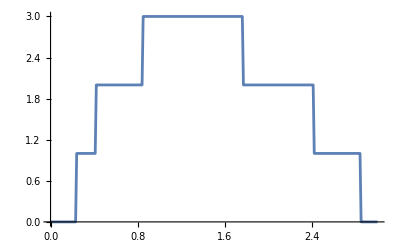

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[00,3,0.01]}]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,7](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,100,8,14](*,s[38,50,1,37]*)],total-concentration]],First],1000]
```

```mathematica
dist[50,25][[1]]
```

{{1,1},{1,2},{1,8},{2,4},{3,10},{4,2},{4,3},{10,1},{16,2},{17,13},{20,11},{21,9},{22,3},{26,14},{31,13},{34,13},{36,10},{41,11},{43,11},{44,7},{46,12},{51,6},{52,4},{54,10},{58,10},{59,5},{59,8},{60,8},{61,3},{64,9},{67,14},{70,7},{71,3},{74,10},{75,11},{77,3},{85,3},{86,9},{88,8},{89,2},{90,12},{91,3},{91,12},{91,13},{92,3},{92,6},{94,6},{95,6},{97,1},{98,5}}

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
misfit[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:=misfit[ω,δ,t,ϵ,ϵ1,total,concentration,number]=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].ConjugateTranspose[Tin].J.Tin].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];tra]
```

```mathematica
misfit[1,0.0001,1,0,0.5,50,25,1]
```

0.57624

```mathematica
ListLinePlot[Table[misfit[ω,0.0001,1,0,.5,50,25,1],{ω,Range[0,1.5,0.01]}],PlotStyle->Directive[Dashed,Black]]
```

```mathematica
Export["~/Desktop/Thesis/transmission.dat",Table[{ω,misfit[ω,0.0001,1,0,.5,50,25,1]},{ω,Range[0,3,0.01]}]]
```

~/Desktop/Thesis/transmission.dat

```mathematica
Position[%54,Min[%54]]
```

{{1,23}}

```mathematica
transmission100=Table[Import["/home/shardul/Downloads/ribbon_analysis/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,190,2]}]
```

```mathematica
transmission100=Table[Import["~/Downloads/mostimp/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"]//Transpose,{x,Range[1,100,2]}]
```

```mathematica
Dimensions[transmission100]
```

{50,301,2}

```mathematica
Table[Transpose[Join[Transpose[Import["~/Downloads/mostimp/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"]],{Table[x,301]}]],{x,Range[1,100,2]}]
```

```mathematica
list:=Table[Transpose[Join[{transmission100[[x]][[1]][[;;100]]},{transmission100[[x]][[2]][[;;100]]},{Table[x,100]}]],{x,50}]
```

```mathematica
list2:=Flatten[list,1]
```

```mathematica
list2
```

```mathematica
cy=Interpolation[list2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Table[{x,y,Abs[cy[x,y]]},{x,Range[0,1,0.1]},{y,Range[0.01,0.99,0.1]}]
```

InterpolatingFunction::femdmval: Input value {0.,0.01} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,0.11} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,0.21} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

{{{0.,0.01,1.},{0.,0.11,1.},{0.,0.21,1.},{0.,0.31,1.},{0.,0.41,1.},{0.,0.51,1.},{0.,0.61,1.},{0.,0.71,1.},{0.,0.81,1.},{0.,0.91,1.}},{{0.1,0.01,47.4062},{0.1,0.11,3.75565},{0.1,0.21,2.1558},{0.1,0.31,1.34853},{0.1,0.41,1.},{0.1,0.51,1.},{0.1,0.61,1.},{0.1,0.71,1.},{0.1,0.81,1.},{0.1,0.91,1.}},{{0.2,0.01,48.2836},{0.2,0.11,21.4952},{0.2,0.21,6.75608},{0.2,0.31,4.63971},{0.2,0.41,3.4144},{0.2,0.51,2.46664},{0.2,0.61,1.75463},{0.2,0.71,1.17883},{0.2,0.81,1.},{0.2,0.91,1.}},{{0.3,0.01,24.2918},{0.3,0.11,46.947},{0.3,0.21,49.521},{0.3,0.31,48.2409},{0.3,0.41,37.2381},{0.3,0.51,26.},{0.3,0.61,17.6109},{0.3,0.71,11.4954},{0.3,0.81,7.252},{0.3,0.91,3.18676}},{{0.4,0.01,82.7481},{0.4,0.11,5.73005},{0.4,0.21,48.7191},{0.4,0.31,48.3409},{0.4,0.41,49.8137},{0.4,0.51,33.6872},{0.4,0.61,23.0977},{0.4,0.71,15.456},{0.4,0.81,9.64074},{0.4,0.91,4.70591}},{{0.5,0.01,141.204},{0.5,0.11,64.1863},{0.5,0.21,12.8318},{0.5,0.31,48.4677},{0.5,0.41,48.0895},{0.5,0.51,48.574},{0.5,0.61,34.8092},{0.5,0.71,28.},{0.5,0.81,22.89},{0.5,0.91,19.}},{{0.6,0.01,199.66},{0.6,0.11,122.642},{0.6,0.21,45.6245},{0.6,0.31,31.3936},{0.6,0.41,48.2162},{0.6,0.51,48.4749},{0.6,0.61,49.8328},{0.6,0.71,44.8732},{0.6,0.81,38.2276},{0.6,0.91,31.742}},{{0.7,0.01,258.117},{0.7,0.11,181.099},{0.7,0.21,104.081},{0.7,0.31,27.0627},{0.7,0.41,47.7138},{0.7,0.51,48.1032},{0.7,0.61,49.3729},{0.7,0.71,49.666},{0.7,0.81,48.4694},{0.7,0.91,40.1252}},{{0.8,0.01,316.573},{0.8,0.11,239.555},{0.8,0.21,162.537},{0.8,0.31,85.5189},{0.8,0.41,8.50086},{0.8,0.51,48.0916},{0.8,0.61,49.3814},{0.8,0.71,47.6795},{0.8,0.81,49.9465},{0.8,0.91,45.5401}},{{0.9,0.01,375.029},{0.9,0.11,298.011},{0.9,0.21,220.993},{0.9,0.31,143.975},{0.9,0.41,66.9571},{0.9,0.51,10.0609},{0.9,0.61,49.1961},{0.9,0.71,28.6586},{0.9,0.81,24.3065},{0.9,0.91,20.7121}},{{1.,0.01,433.485},{1.,0.11,356.467},{1.,0.21,279.449},{1.,0.31,202.431},{1.,0.41,125.413},{1.,0.51,48.3953},{1.,0.61,109.392},{1.,0.71,50.},{1.,0.81,53.2541},{1.,0.91,51.1296}}}

```mathematica
cy[0.1,-0.5]
```

InterpolatingFunction::femdmval: Input value {0.1,-0.5} lies outside the range of data in the interpolating function.

-5.88882×10^9

```mathematica
ListDensityPlot[list2]
```

```mathematica
ListDensityPlot[list2,PlotLegends->Automatic,DataRange->{{0,1},{-1,1}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]
```

```mathematica
ContourPlot[cy[x,y],{x,0.01,0.99},{y,-1,1},PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]
```

```mathematica
Export["~/con_5.pdf",%85]
```

~/con_5.pdf

```mathematica
ListContourPlot[list2,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{{Transmission,None},{Energy,None}}]
```

```mathematica
ListContourPlot[list2,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{{ΔT,None},{Energy,None}},DataRange->{{0,1},All}]
```

```mathematica
Export["~/Downloads/ribbon_analysis/con_4.pdf",%42]
```

~/Downloads/ribbon_analysis/con_4.pdf

```mathematica
Show[%77,%119]
```

```mathematica
ListContourPlot[%17,InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"Pastel",FrameLabel->{{Energy,None},{Concentration,None}}]
```

```mathematica
Export["~/Downloads/ribbon_analysis/con_3.pdf",%79]
```

~/Downloads/ribbon_analysis/con_3.pdf

```mathematica
Dimensions[transmission100]
```

{95,301,2}

```mathematica
misfit100[n_,x_,y_]:=Module[{m5=Table[{ω,misfit[ω,0.0001,1,0,.5,30,15,1]},{ω,Range[0,0.99,0.01]}]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;100]][[;;,1]],100(m5[[1;;100,2]]-transmission100[[ξ]][[1;;100,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,50}]; 
ρ1]
```

```mathematica
misfit100[0,0,0.99]
```

```mathematica
Table[Show[ListLinePlot[misfit100[n,1.5,0]],ListLinePlot[Table[{50,y},{y,0,1,0.0001}],PlotStyle->Red]],{n,10}]
```

```mathematica
misfit100[3,1.5,0]
```

```mathematica
Export["abs_trans2.dat",ParallelTable[{ω,misfit[ω,0.0001,1,0,.5,50,25,2]},{ω,Range[0,3,0.01]}]]
```

abs_trans2.dat

```mathematica
ListPlot[%38,Joined->True]
```

```mathematica
aa=Table[misfit[0.7,2.5,0],100]
```

```mathematica
bb=Table[Abs[Around[Table[Abs[aa[[x]][[y]]], {x, 100}]]],{y,7}]
```

{1.140.08,0.630.06,0.2580.033,0.330.04,0.290.04,0.2980.034,0.3390.035}

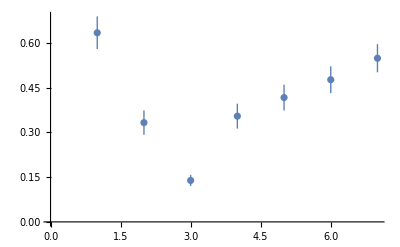

```mathematica
ListPlot[%24]
```

```mathematica
bb=Table[Abs[Around[Table[Abs[aa[[x]][[y]]], {x, 100}]]],{y,7}]
```

```mathematica
cc=Table[Abs[Mean[Table[Abs[aa[[x]][[y]]], {x, 100}]]],{y,7}]
```

{1.13607,0.634637,0.257559,0.327134,0.29274,0.297552,0.338966}

```mathematica
Show[Plot[Interpolation[cc][x],{x,1.,7.}],ListPlot[bb,PlotStyle->Red],PlotRange->{{1,7},{0.05,1.3}},Frame->True,Axes->False,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}}]
```

```mathematica
ListPlot[aa,Joined->True,Frame->True,Axes->False,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{{HoldForm[Γ],None},{HoldForm[ω],None}},PlotStyle->Red]
```

```mathematica
Interpolation[bb]
```

InterpolatingFunction[…]

```mathematica
%31[1.5]
```

0.490.06

```mathematica
Show[Plot[Interpolation[cc][x],{x,1.,7.}],ListPlot[bb,PlotStyle->Red],PlotRange->{{1,7},{0.05,0.8}},Frame->True,Axes->False,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}}]
```

```mathematica
Table[Abs[Around[Table[Abs[aa[[x]][[y]]], {x, 100}]]],{y,7}]
```

{0.500.06,0.1960.031,0.1150.017,0.1600.025,0.240.04,0.320.05,0.380.06}

```mathematica
ListPlot[Transpose[Join[{Range[0.1,0.7,0.1]},{%151}]],Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},PlotStyle->Blue]
```

```mathematica
Show[%145]
```

```mathematica
ListLinePlot[misfit[0.5,1.8,0]*100]
```

```mathematica
Abs[misfit2[0.5,1.5,0]]
```

Abs[misfit2[0.5,1.5,0]]

```mathematica
aa=Table[misfit2[0.5,1.5,0],50]
```

```mathematica
bb=Table[{y-1,Abs[Around[Table[Abs[%30[[x]][[y]]], {x, 10}]]]},{y,10}]
```

```mathematica
{{0,0.001080.00018},{1,0.008560.00018},{2,0.005430.00018},{3,0.003470.00018},{4,0.001+0.001200.00018},{5,0.001200.00018},{6,0.000540.00018},{7,0.000140.00011},{8,0.000610.00018},{9,0.000870.00018}}
```

```mathematica
{{1,0.008560.00018},{2,0.005430.00018},{3,0.003470.00018},{4,0.002200.00018},{5,0.001200.00018},{6,0.000540.00018},{7,0.000140.00011},{8,0.000610.00018},{9,0.000870.00018}}
```

{{1,0.008560.00018},{2,0.005430.00018},{3,0.003470.00018},{4,0.002200.00018},{5,0.001200.00018},{6,0.000540.00018},{7,0.000140.00011},{8,0.000610.00018},{9,0.000870.00018}}

```mathematica
Show[ListPlot[%35,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[n,0.5]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}],ListLinePlot[{Table[{7,y},{y,Range[0,2,0.005]}],Table[{7,y},{y,Range[0.0,2,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

-Graphics-

```mathematica
ListPlot[bb,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[3,ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},PlotRange->All]
```

```mathematica
Show[%205,%207,PlotRange->All]
```

-Graphics-

```mathematica
Show[%209,FrameLabel->{{HoldForm[HoldForm[χ]],None},{HoldForm[ϵ],RawBoxes[RowBox[{RowBox[{"Red","~","old"}]," ","misfit"," ","function"}]]}},PlotLabel->None]
```

```mathematica
ListPlot[bb,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[3,ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
ListPlot[bb,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[3,ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%188,%193]
```

```mathematica
Show[%194,FrameLabel->{{HoldForm[HoldForm[χ]],None},{HoldForm[n],HoldForm[Red #misfit function (min=4)]}},PlotLabel->None]
```

```mathematica
Show[%194,FrameLabel->{{HoldForm[HoldForm[χ]],None},{HoldForm[n],None}},PlotLabel->None]
```

```mathematica
ListPlot[bb,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[3,ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
aa=Table[misfit2[0.5,2.5,0],10]
```

```mathematica
Transpose[Join[{Range[1,7,1]*15},{bb}]]
```

{{15,0.680.06},{30,0.2640.033},{45,0.1510.018},{60,0.1380.015},{75,0.1630.020},{90,0.1970.025},{105,0.1970.024}}

```mathematica
bb=Table[Abs[Around[Table[Abs[aa[[x]][[y]]], {x, 10}]]],{y,7}]*100
```

{0.680.06,0.2640.033,0.1510.018,0.1380.015,0.1630.020,0.1970.025,0.1970.024}

```mathematica
cc=Table[Abs[Mean[Table[Abs[aa[[x]][[y]]], {x, 10}]]],{y,7}]*100
```

{0.678985,0.264356,0.150616,0.137952,0.162766,0.197165,0.196548}

InterpolatingFunction::dmval: Input value {1.00217} lies outside the range of data in the interpolating function. Extrapolation will be used.

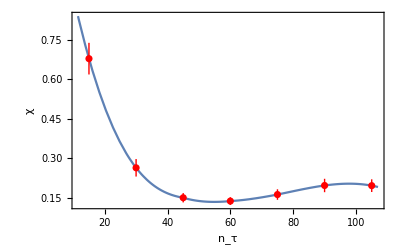

```mathematica
Show[Plot[Interpolation[Transpose[Join[{Range[1,7,1]*15},{cc}]]][x],{x,1,107}],ListPlot[Transpose[Join[{Range[1,7,1]*15},{bb}]],PlotStyle->Red],PlotRange->All,Frame->True,Axes->False,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n_τ],None}}]
```

```mathematica
data11=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/"<>ToString[x]<>"imp/"<>ToString[x]<>"imp5.csv"],{x,7}]
```

{1}
 |  |  |  |

```mathematica
misfit2[0.5,2.5,0]
```

Import::nffil: File /home/shardulmukim/PhD/data/data/14imp100.csv not found during Import.

Part::take: Cannot take positions 1 through 300 in $Failed.

Part::partd: Part specification $Failed⟦1;;300,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/PhD/data/data/28imp100.csv not found during Import.

Part::take: Cannot take positions 1 through 300 in $Failed.

Part::partd: Part specification $Failed⟦1;;300,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/PhD/data/data/42imp100.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 300 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1;;300,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.004 (0.01 (10000. Abs[2.83264×10^-7-1. $Failed⟦1;;300,1;;All⟧⟦1;;All,2⟧]^2-0.01 (-0.01 (0.125 (-100. (-33.3333 (10000. Abs[2.0696×10^-7-1. $Failed⟦1⟧⟦1⟧]^2-10000. Abs[2.87439×10^-7-1]^2)-50. (-10000. (Abs11])^2+1))-100. (1))+1/3 (1))+1/2 (1)))+248+0.01 (1-1)),7,0.004 1}
 |  |  |  |

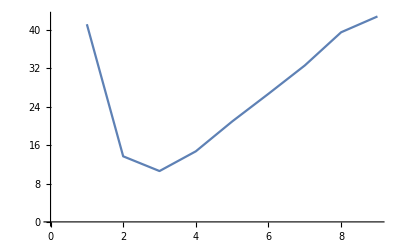

```mathematica
ListLinePlot[misfit2[0.5,1.5,0]]
```

```mathematica
aa=Table[misfit2[0.5,1.5,0],100]
```

{{0.45877,0.16782,0.124482,0.158159,0.216206,0.277121,0.340448,0.413387,0.448821},{0.602666,0.254671,0.168799,0.174453,0.215151,0.255199,0.298858,0.348998,0.377153},{0.511966,0.182167,0.116147,0.134012,0.17996,0.229259,0.282684,0.342979,0.374361},{0.584879,0.224724,0.137535,0.138926,0.172269,0.211352,0.25447,0.305202,0.331957},{0.414854,0.130681,0.102419,0.150924,0.220568,0.287763,0.355677,0.442058,0.481778},{0.517889,0.182678,0.112642,0.129052,0.176232,0.223733,0.274259,0.334982,0.363585},{0.487008,0.180312,0.124516,0.148784,0.201118,0.256903,0.316443,0.386338,0.419622},{0.368024,0.112097,0.097946,0.151759,0.221218,0.283504,0.346369,0.422938,0.458101},{0.429895,0.150987,0.117676,0.158632,0.220274,0.284253,0.352085,0.43326,0.473574},{0.502386,0.184361,0.126986,0.15201,0.204493,0.257091,0.310557,0.373898,0.405017},{0.436503,0.13829,0.0988156,0.137347,0.201124,0.263222,0.326226,0.39837,0.4328},{0.466904,0.176671,0.128806,0.164147,0.224081,0.280393,0.335314,0.401255,0.435751},{0.454644,0.134423,0.0781967,0.106107,0.160624,0.216478,0.276085,0.344197,0.377048},{0.504601,0.18376,0.115805,0.134138,0.182649,0.229445,0.279961,0.342496,0.374548},{0.63076,0.237901,0.136653,0.13503,0.169268,0.207569,0.250676,0.306923,0.331855},{0.396147,0.128723,0.101489,0.146861,0.210303,0.272944,0.338387,0.416901,0.452048},{0.456152,0.149579,0.104683,0.139878,0.195274,0.25009,0.305986,0.373139,0.404205},{0.350871,0.108732,0.103076,0.163721,0.237154,0.304771,0.372865,0.451031,0.488917},{0.444397,0.146346,0.104417,0.142094,0.20493,0.263983,0.320966,0.391321,0.424092},{0.405696,0.136185,0.112052,0.162356,0.230521,0.296019,0.364449,0.445994,0.484033},{0.606512,0.232305,0.13637,0.14087,0.181734,0.224168,0.270902,0.322504,0.350932},{0.391745,0.141053,0.123554,0.17587,0.242932,0.309366,0.380333,0.46274,0.502345},{0.557756,0.19917,0.108142,0.109589,0.145587,0.185261,0.230256,0.287625,0.318063},{0.414469,0.1254,0.0893634,0.127653,0.190816,0.251651,0.313234,0.389295,0.423955},{0.459378,0.169094,0.132759,0.176484,0.243308,0.305997,0.369975,0.447539,0.483513},{0.338325,0.112345,0.115861,0.183465,0.265938,0.33925,0.41011,0.494307,0.534436},{0.526493,0.181512,0.107401,0.121517,0.164167,0.208691,0.257165,0.320676,0.350464},{0.458289,0.160534,0.114664,0.143627,0.197433,0.251206,0.305543,0.37534,0.406962},{0.462707,0.153316,0.10012,0.126992,0.180403,0.234779,0.293321,0.361139,0.394021},{0.524711,0.17613,0.0967698,0.107589,0.149434,0.195793,0.247253,0.312954,0.344889},{0.432219,0.136076,0.103372,0.149339,0.21575,0.279129,0.341803,0.420901,0.456533},{0.454459,0.140262,0.0832342,0.106915,0.155696,0.208206,0.263283,0.330256,0.361519},{0.465386,0.150718,0.0960913,0.12151,0.171755,0.22262,0.275818,0.342153,0.373161},{0.56781,0.207256,0.125032,0.137492,0.182921,0.227533,0.275905,0.335026,0.363727},{0.41745,0.134851,0.104474,0.146666,0.20932,0.268123,0.328134,0.398386,0.430322},{0.412611,0.133912,0.110139,0.161414,0.236603,0.304698,0.368461,0.447266,0.483218},{0.391268,0.173183,0.17339,0.239906,0.322545,0.394544,0.464819,0.550737,0.591308},{0.496776,0.15824,0.0924362,0.11496,0.168155,0.221131,0.275693,0.342068,0.373399},{0.390272,0.14731,0.137054,0.19055,0.261397,0.326503,0.395912,0.479848,0.520002},{0.53245,0.208191,0.143667,0.166117,0.216641,0.265389,0.318288,0.378044,0.40791},{0.663236,0.256157,0.142275,0.12866,0.14969,0.180474,0.217346,0.261099,0.284343},{0.343224,0.18006,0.227252,0.321798,0.421832,0.505382,0.587717,0.690948,0.735874},{0.446283,0.145309,0.100683,0.130579,0.184047,0.235209,0.29048,0.361711,0.393916},{0.482979,0.17147,0.121037,0.146492,0.197071,0.246023,0.299599,0.365071,0.39739},{0.586958,0.215079,0.12477,0.126686,0.158138,0.196152,0.24016,0.293453,0.319418},{0.531598,0.191713,0.113634,0.122727,0.165612,0.210201,0.259499,0.320442,0.350214},{0.492185,0.176084,0.115493,0.144177,0.200522,0.257015,0.317089,0.387598,0.421521},{0.518018,0.19013,0.127647,0.14716,0.193416,0.240569,0.292408,0.355797,0.386189},{0.458888,0.136274,0.0795907,0.108258,0.158779,0.211987,0.267464,0.336158,0.368369},{0.550217,0.201492,0.120139,0.12332,0.15914,0.200135,0.247772,0.30435,0.332002},{0.481973,0.181939,0.133644,0.164219,0.218263,0.266935,0.3157,0.374271,0.403489},{0.442289,0.157764,0.122943,0.159944,0.217651,0.272433,0.328347,0.402994,0.4359},{0.4303,0.141522,0.108186,0.152173,0.216612,0.277232,0.339261,0.414546,0.44979},{0.454082,0.159145,0.112104,0.146459,0.202764,0.256748,0.313196,0.382054,0.417594},{0.537173,0.176968,0.1002,0.115121,0.156581,0.20182,0.250377,0.310952,0.339039},{0.533397,0.179871,0.100422,0.109063,0.145493,0.187664,0.232168,0.28763,0.315666},{0.421438,0.149559,0.117341,0.159501,0.221956,0.285202,0.352108,0.430118,0.466669},{0.53682,0.191958,0.113639,0.127347,0.171242,0.216546,0.263534,0.323486,0.351916},{0.57498,0.203399,0.11214,0.118806,0.160681,0.207118,0.258878,0.31916,0.348711},{0.432261,0.147891,0.11589,0.159163,0.221237,0.279976,0.339459,0.412857,0.446032},{0.383764,0.136535,0.132758,0.194151,0.273084,0.343307,0.413074,0.501918,0.541984},{0.499371,0.178081,0.121645,0.141833,0.187074,0.232657,0.279452,0.335854,0.364008},{0.507157,0.182079,0.115437,0.137073,0.186711,0.241598,0.299956,0.367293,0.401933},{0.382651,0.144445,0.144002,0.215031,0.305596,0.381752,0.454699,0.544219,0.584222},{0.492226,0.17448,0.122352,0.153019,0.208451,0.264798,0.323117,0.394395,0.427124},{0.444283,0.149219,0.10376,0.132872,0.181445,0.231627,0.282425,0.34676,0.377186},{0.373595,0.137871,0.131947,0.190777,0.262964,0.329943,0.397374,0.478376,0.515534},{0.595865,0.245018,0.16898,0.181399,0.225007,0.270759,0.317319,0.372772,0.399569},{0.454045,0.140661,0.086704,0.11325,0.166489,0.2194,0.27405,0.337864,0.369813},{0.566182,0.203289,0.121153,0.128806,0.167097,0.208764,0.254137,0.307861,0.335944},{0.454888,0.146571,0.0980949,0.128573,0.180981,0.231885,0.286636,0.355343,0.387196},{0.398203,0.13021,0.107173,0.155016,0.222298,0.286155,0.351266,0.427791,0.464237},{0.594836,0.225389,0.136302,0.136419,0.169649,0.207174,0.249525,0.302085,0.328387},{0.46226,0.152829,0.103749,0.133259,0.185242,0.235897,0.288275,0.355477,0.386293},{0.585143,0.230149,0.152281,0.162041,0.199856,0.244311,0.291049,0.35227,0.380179},{0.481688,0.176807,0.125899,0.154576,0.205471,0.262522,0.322444,0.39135,0.426312},{0.418144,0.161966,0.144876,0.201294,0.276785,0.347573,0.42031,0.501826,0.53862},{0.555798,0.20975,0.131453,0.140537,0.175949,0.217379,0.26239,0.322605,0.352322},{0.440624,0.163021,0.130891,0.172159,0.236478,0.296031,0.355913,0.432585,0.469154},{0.538723,0.191246,0.118738,0.135186,0.180016,0.229328,0.286085,0.357376,0.390864},{0.529221,0.204029,0.138085,0.154645,0.20192,0.24942,0.300133,0.365152,0.396731},{0.534035,0.187407,0.115793,0.133446,0.180807,0.231249,0.283014,0.344093,0.373905},{0.476313,0.159109,0.107492,0.136691,0.187665,0.239592,0.290935,0.357965,0.388188},{0.63416,0.283209,0.194539,0.191092,0.219172,0.25321,0.297431,0.350926,0.379237},{0.486001,0.168151,0.112282,0.14216,0.201898,0.260049,0.317908,0.38478,0.418255},{0.504184,0.216096,0.168221,0.197635,0.25402,0.303326,0.35218,0.417904,0.449825},{0.536919,0.218918,0.151909,0.170831,0.217766,0.263364,0.312814,0.375892,0.408224},{0.482603,0.171948,0.124382,0.154946,0.208453,0.260514,0.313278,0.377506,0.407945},{0.405271,0.132168,0.11635,0.174597,0.250283,0.321954,0.393064,0.478436,0.517546},{0.490895,0.186414,0.136724,0.160886,0.2059,0.250906,0.296461,0.35524,0.383193},{0.504922,0.18633,0.128667,0.155033,0.203959,0.253556,0.303896,0.366952,0.397933},{0.495344,0.164029,0.101331,0.120852,0.170404,0.220047,0.273126,0.341777,0.374868},{0.492794,0.19582,0.151708,0.188286,0.249427,0.306085,0.363396,0.432329,0.465714},{0.380491,0.149955,0.145363,0.206466,0.28198,0.352,0.425211,0.516561,0.557158},{0.410412,0.144091,0.12326,0.176659,0.253214,0.321512,0.390277,0.469592,0.506755},{0.45744,0.169537,0.135923,0.175942,0.237521,0.296881,0.358172,0.429684,0.463927},{0.468751,0.178886,0.135755,0.168975,0.221695,0.27248,0.325238,0.384114,0.414328},{0.459355,0.151721,0.105858,0.141425,0.200521,0.256749,0.312569,0.382442,0.415372},{0.532804,0.195111,0.122452,0.132051,0.168642,0.209331,0.252857,0.308637,0.336332},{0.460865,0.163346,0.119322,0.151795,0.202453,0.255311,0.309396,0.375259,0.407284}}

```mathematica
Table[{y,Around[Table[Sqrt[Abs[aa[[x]][[y]]]], {x, 100}]]},{y,9}]
```

{{1,0.690.05},{2,0.410.04},{3,0.3470.032},{4,0.390.04},{5,0.450.04},{6,0.510.05},{7,0.560.05},{8,0.620.05},{9,0.640.05}}

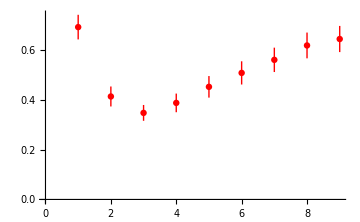

```mathematica
ListPlot[%27,PlotStyle->Red]
```

```mathematica
Interpolation[Table[{y,Mean[Table[Abs[%65[[x]][[y]]], {x, 50}]]},{y,9}]]
```

InterpolatingFunction[…]

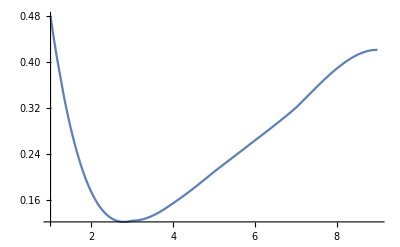

```mathematica
Plot[%67[x],{x,1.,9.}]
```

```mathematica
%96[4]
```

0.1540.021

```mathematica
Table[{x,InterpolatingFunction[…][x]},{x,Range[1,9,0.05]}]
```

{{1.,0.479165},{1.05,0.455055},{1.1,0.432004},{1.15,0.409992},{1.2,0.388995},{1.25,0.368992},{1.3,0.34996},{1.35,0.331879},{1.4,0.314725},{1.45,0.298476},{1.5,0.283111},{1.55,0.268608},{1.6,0.254944},{1.65,0.242098},{1.7,0.230047},{1.75,0.218769},{1.8,0.208242},{1.85,0.198445},{1.9,0.189355},{1.95,0.18095},{2.,0.173208},{2.05,0.166107},{2.1,0.159625},{2.15,0.15374},{2.2,0.14843},{2.25,0.143672},{2.3,0.139446},{2.35,0.135728},{2.4,0.132497},{2.45,0.129731},{2.5,0.127407},{2.55,0.125504},{2.6,0.123999},{2.65,0.122871},{2.7,0.122097},{2.75,0.121656},{2.8,0.121525},{2.85,0.121682},{2.9,0.122106},{2.95,0.122773},{3.,0.123663},{3.05,0.123752},{3.1,0.124034},{3.15,0.124503},{3.2,0.12515},{3.25,0.12597},{3.3,0.126954},{3.35,0.128097},{3.4,0.129391},{3.45,0.130829},{3.5,0.132404},{3.55,0.134109},{3.6,0.135937},{3.65,0.137882},{3.7,0.139935},{3.75,0.142091},{3.8,0.144342},{3.85,0.146681},{3.9,0.149101},{3.95,0.151595},{4.,0.154157},{4.05,0.156513},{4.1,0.158926},{4.15,0.161393},{4.2,0.163911},{4.25,0.166478},{4.3,0.169089},{4.35,0.171743},{4.4,0.174436},{4.45,0.177165},{4.5,0.179928},{4.55,0.18272},{4.6,0.18554},{4.65,0.188383},{4.7,0.191248},{4.75,0.194132},{4.8,0.19703},{4.85,0.19994},{4.9,0.20286},{4.95,0.205786},{5.,0.208715},{5.05,0.21143},{5.1,0.214145},{5.15,0.21686},{5.2,0.219577},{5.25,0.222294},{5.3,0.225013},{5.35,0.227734},{5.4,0.230456},{5.45,0.23318},{5.5,0.235907},{5.55,0.238636},{5.6,0.241367},{5.65,0.244102},{5.7,0.246839},{5.75,0.24958},{5.8,0.252325},{5.85,0.255073},{5.9,0.257826},{5.95,0.260582},{6.,0.263343},{6.05,0.266041},{6.1,0.268745},{6.15,0.271456},{6.2,0.274176},{6.25,0.276905},{6.3,0.279646},{6.35,0.282398},{6.4,0.285164},{6.45,0.287945},{6.5,0.290742},{6.55,0.293556},{6.6,0.296388},{6.65,0.29924},{6.7,0.302113},{6.75,0.305008},{6.8,0.307927},{6.85,0.31087},{6.9,0.313839},{6.95,0.316836},{7.,0.31986},{7.05,0.323393},{7.1,0.326949},{7.15,0.330523},{7.2,0.334109},{7.25,0.337701},{7.3,0.341293},{7.35,0.344879},{7.4,0.348453},{7.45,0.352009},{7.5,0.355541},{7.55,0.359044},{7.6,0.362511},{7.65,0.365936},{7.7,0.369314},{7.75,0.372639},{7.8,0.375904},{7.85,0.379104},{7.9,0.382232},{7.95,0.385284},{8.,0.388252},{8.05,0.391131},{8.1,0.393915},{8.15,0.396598},{8.2,0.399175},{8.25,0.401638},{8.3,0.403983},{8.35,0.406202},{8.4,0.408292},{8.45,0.410244},{8.5,0.412055},{8.55,0.413716},{8.6,0.415223},{8.65,0.41657},{8.7,0.417751},{8.75,0.418759},{8.8,0.41959},{8.85,0.420236},{8.9,0.420692},{8.95,0.420952},{9.,0.42101}}

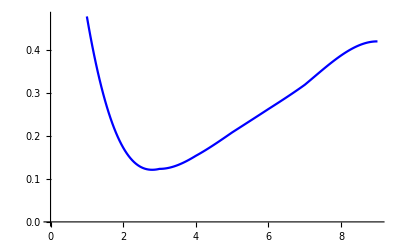

```mathematica
ListPlot[%69,Joined->True,PlotStyle->Blue]
```

```mathematica
ListLinePlot[%105,PlotStyle->Blue]
```

-Graphics-

```mathematica
Table[{y,Mean[Table[Abs[aa[[x]][[y]]], {x, 50}]]},{y,9}]
```

{{1,0.479165},{2,0.173208},{3,0.123663},{4,0.154157},{5,0.208715},{6,0.263343},{7,0.31986},{8,0.388252},{9,0.42101}}

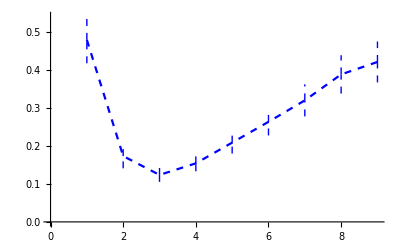

```mathematica
ListLinePlot[%50,PlotStyle->{Dashed,Blue}]
```

```mathematica
ListPlot[%66,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
ListPlot[%66,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

```mathematica
Show[%81,Frame->True,PlotRange->{{0,9},{0.05,0.56}},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[ListLinePlot[%105,PlotStyle->{Blue},PlotRange->All,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6},None},{{0,2,4,6,8},None}}],ListPlot[%50,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6},None},{{0,2,4,6,8},None}},PlotRange->All],ListPlot[%66,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6},None},{{0,2,4,6,8},None}},PlotRange->All],ListLinePlot[{Table[{3,y},{y,Range[0,0.3,0.005]}],Table[{3,y},{y,Range[0.31,0.6,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dotted,Black}},PlotRange->All,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6},None},{{0,2,4,6,8},None}}],Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
ColorData["StarryNightColors","ColorFunction"]
```

ColorDataFunction[…]

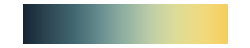

```mathematica
ColorData["StarryNightColors","Panel"]
```

```mathematica
ColorData["StarryNightColors","Panel"]
```

-Graphics-

```mathematica
ColorData["BlueGreenYellow"]
```

ColorDataFunction[…]

```mathematica
ColorData["BlueGreenYellow","Range"]
```

{0,1}

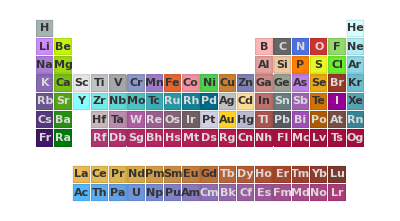

```mathematica
ColorData["Atoms","Panel"]
```

```mathematica
ColorData["Atoms","Range"]
```

{{H,He,Li,Be,B,C,N,O,F,Ne,Na,Mg,Al,Si,P,S,Cl,Ar,K,Ca,Sc,Ti,V,Cr,Mn,Fe,Co,Ni,Cu,Zn,Ga,Ge,As,Se,Br,Kr,Rb,Sr,Y,Zr,Nb,Mo,Tc,Ru,Rh,Pd,Ag,Cd,In,Sn,Sb,Te,I,Xe,Cs,Ba,La,Ce,Pr,Nd,Pm,Sm,Eu,Gd,Tb,Dy,Ho,Er,Tm,Yb,Lu,Hf,Ta,W,Re,Os,Ir,Pt,Au,Hg,Tl,Pb,Bi,Po,At,Rn,Fr,Ra,Ac,Th,Pa,U,Np,Pu,Am,Cm,Bk,Cf,Es,Fm,Md,No,Lr,Rf,Db,Sg,Bh,Hs,Mt,Ds,Rg,Cn,Nh,Fl,Mc,Lv,Ts,Og}}

```mathematica
ContourPlot[Interpolation[%98][x,y],{x,0.3,0.9},{y,1,5},PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]
```

```mathematica
Join[ab[[1]],ab[[2]],ab[[3]],ab[[4]],ab[[5]],ab[[6]],ab[[7]]]
```

{{0.3,1,-2.75078×10^8},{0.4,1,-8.81086×10^8},{0.5,1,-3.0157×10^9},{0.6,1,-8.89057×10^9},{0.7,1,-2.024×10^10},{0.8,1,-2.74319×10^10},{0.9,1,-2.5352×10^10},{0.3,2,-1.00893×10^9},{0.4,2,-5.88088×10^9},{0.5,2,-2.96816×10^10},{0.6,2,-4.58763×10^10},{0.7,2,-2.90154×10^10},{0.8,2,-1.47796×10^10},{0.9,2,-8.42355×10^9},{0.3,3,-2.94995×10^9},{0.4,3,-2.29662×10^10},{0.5,3,-5.77608×10^10},{0.6,3,-2.76931×10^10},{0.7,3,-1.17908×10^10},{0.8,3,-6.4012×10^9},{0.9,3,-4.338×10^9},{0.3,4,-7.14759×10^9},{0.4,4,-4.90007×10^10},{0.5,4,-3.62211×10^10},{0.6,4,-1.36085×10^10},{0.7,4,-6.33935×10^9},{0.8,4,-4.07136×10^9},{0.9,4,-3.16968×10^9},{0.3,5,-1.49488×10^10},{0.4,5,-5.86574×10^10},{0.5,5,-1.95499×10^10},{0.6,5,-8.2004×10^9},{0.7,5,-4.46712×10^9},{0.8,5,-3.22526×10^9},{0.9,5,-2.72375×10^9},{0.3,6,-2.60491×10^10},{0.4,6,-4.94657×10^10},{0.5,6,-1.1807×10^10},{0.6,6,-5.68613×10^9},{0.7,6,-3.56584×10^9},{0.8,6,-2.82661×10^9},{0.9,6,-2.55592×10^9},{0.3,7,-1.94367×10^10},{0.4,7,-5.64809×10^10},{0.5,7,-7.59625×10^9},{0.6,7,-6.89479×10^9},{0.7,7,-4.03698×10^9},{0.8,7,-3.01901×10^9},{0.9,7,-2.61151×10^9}}

```mathematica
Transpose[%98][[3]]
```

{-2.75078×10^8,-8.81086×10^8,-3.0157×10^9,-8.89057×10^9,-2.024×10^10,-2.74319×10^10,-2.5352×10^10,-1.00893×10^9,-5.88088×10^9,-2.96816×10^10,-4.58763×10^10,-2.90154×10^10,-1.47796×10^10,-8.42355×10^9,-2.94995×10^9,-2.29662×10^10,-5.77608×10^10,-2.76931×10^10,-1.17908×10^10,-6.4012×10^9,-4.338×10^9,-7.14759×10^9,-4.90007×10^10,-3.62211×10^10,-1.36085×10^10,-6.33935×10^9,-4.07136×10^9,-3.16968×10^9,-1.49488×10^10,-5.86574×10^10,-1.95499×10^10,-8.2004×10^9,-4.46712×10^9,-3.22526×10^9,-2.72375×10^9,-2.60491×10^10,-4.94657×10^10,-1.1807×10^10,-5.68613×10^9,-3.56584×10^9,-2.82661×10^9,-2.55592×10^9,-1.94367×10^10,-5.64809×10^10,-7.59625×10^9,-6.89479×10^9,-4.03698×10^9,-3.01901×10^9,-2.61151×10^9}

```mathematica
Export["cont.csv",%98]
```

cont.csv

```mathematica
Export["contc.csv",%106]
```

contc.csv

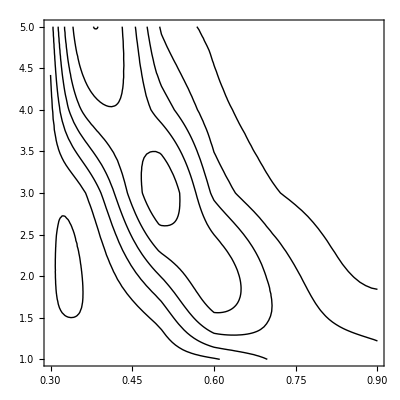

```mathematica
ContourPlot[Interpolation[%98][x,y],{x,0.3,0.9},{y,1,5},ContourShading->]
```

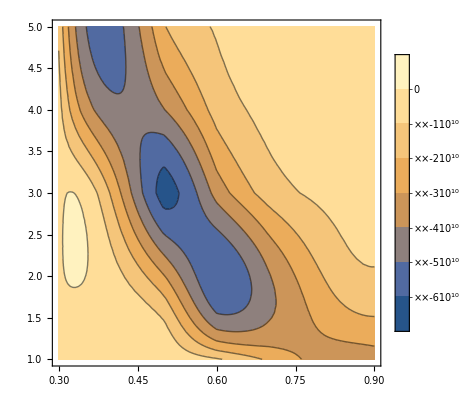

```mathematica
ContourPlot[xy[x,y],{x,0.3,0.9},{y,1,5},PlotTheme->"Detailed"]
```

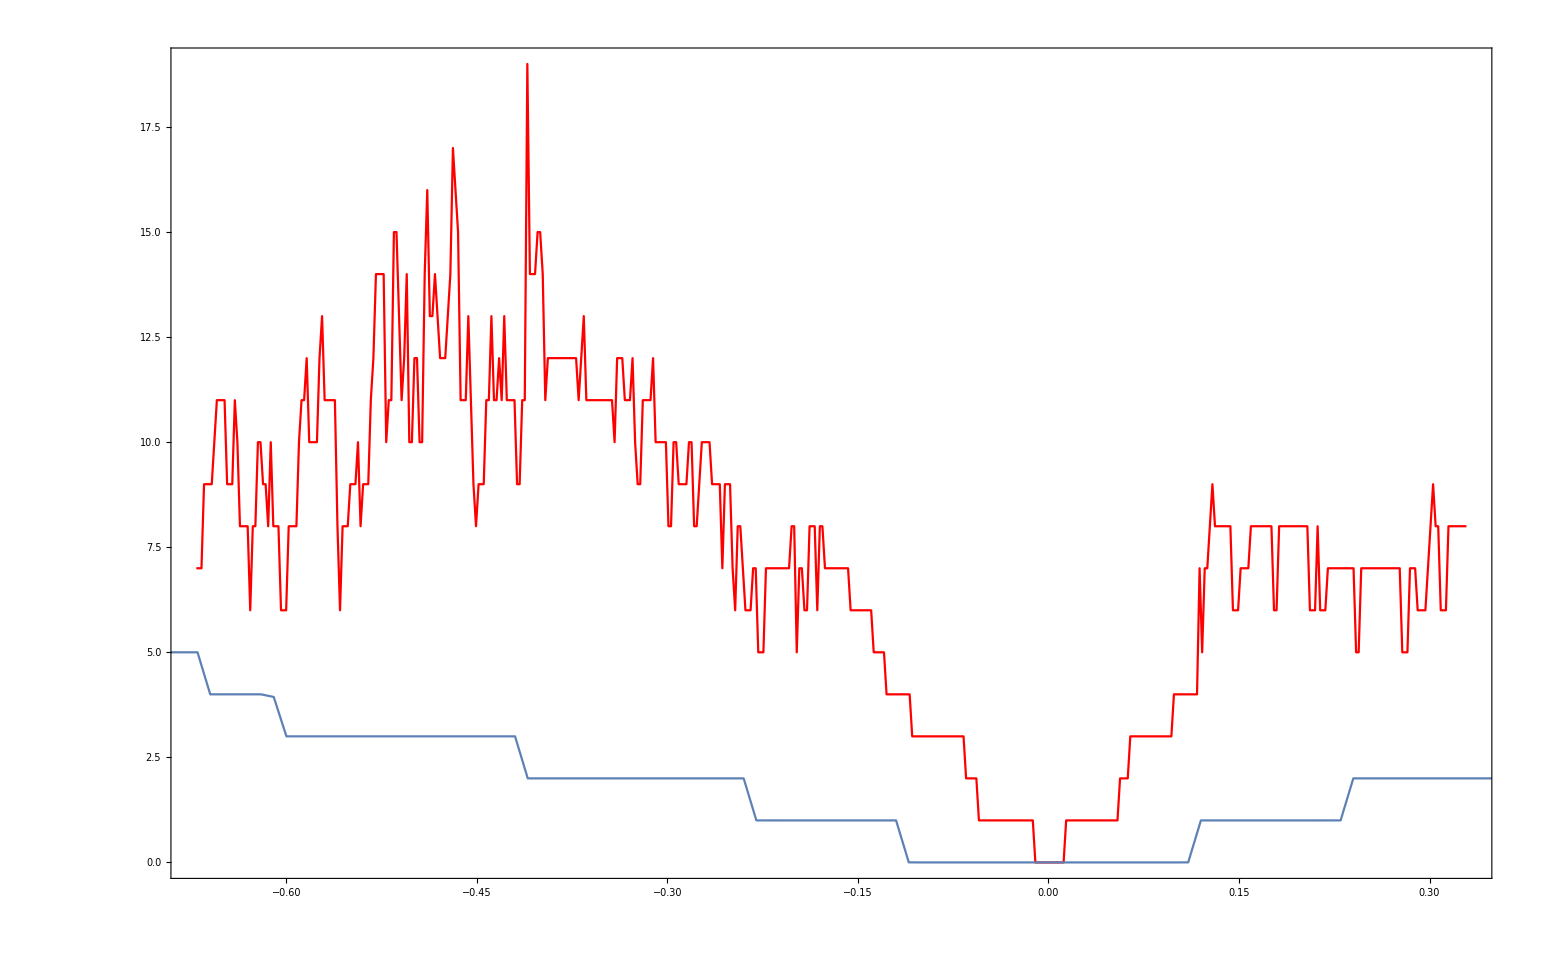

```mathematica
Show[%8,%2]
```

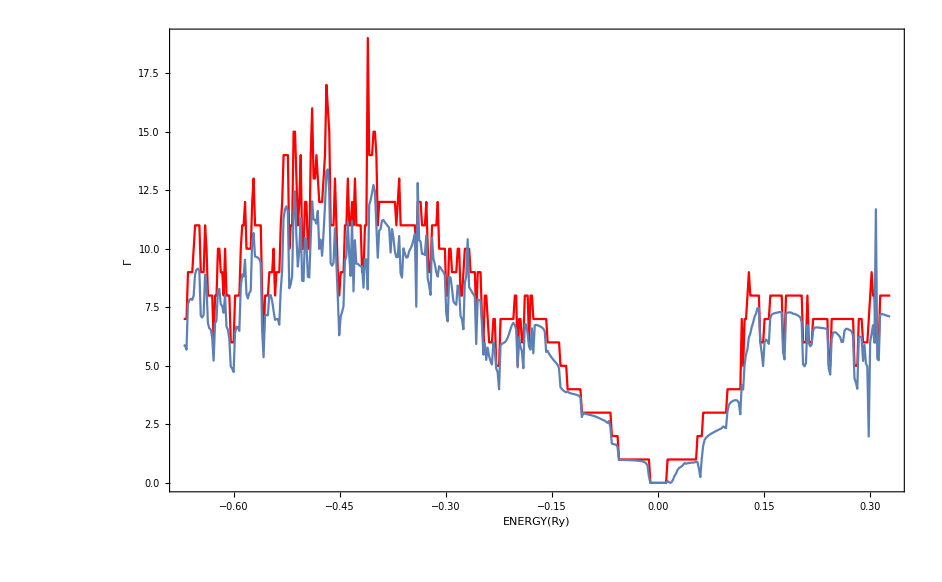

```mathematica
Show[%143,%78,FrameLabel->{{HoldForm[Γ],None},{HoldForm[ENERGY[Ry]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
Export["Impurity.dat",%99]
```

Impurity.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Impurity.dat"]]]
```

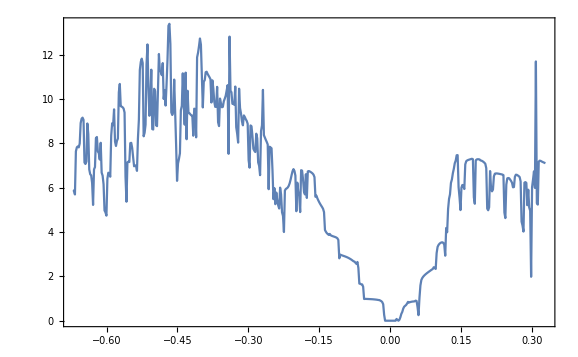

```mathematica
ListPlot[%76,Joined->True,Frame->True]
```

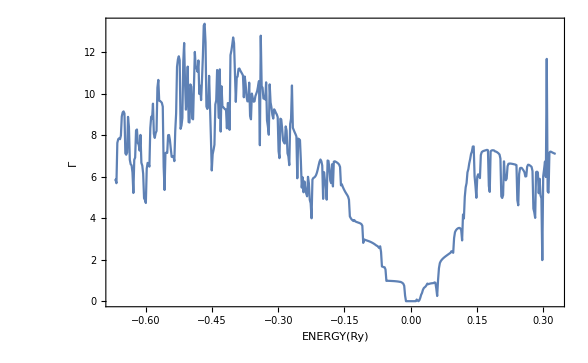

```mathematica
Show[%78,FrameLabel->{{HoldForm[Γ],None},{HoldForm[ENERGY[Ry]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
deltae[ω_,ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={{imp,imp14,imp,imp4,imp12,imp8,imp13,imp,imp12,imp,imp2,imp11,imp,imp10,imp,imp,imp,imp10,imp13,imp5,imp2,imp,imp7,imp,imp,imp2,imp,imp,imp,imp5,imp2,imp4,imp13,imp2,imp,imp,imp,imp,imp1,imp,imp8,imp2,imp5,imp,imp11,imp,imp,imp,imp,imp,imp5,imp,imp,imp8,imp,imp,imp5,imp,imp2,imp,imp,imp,imp13,imp2,imp,imp12,imp,imp,imp,imp,imp1,imp,imp,imp,imp10,imp,imp14,imp,imp,imp13,imp,imp2,imp,imp7,imp,imp,imp,imp8,imp9,imp,imp,imp,imp,imp,imp,imp2,imp7,imp8,imp,imp}};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b];
tra]
```

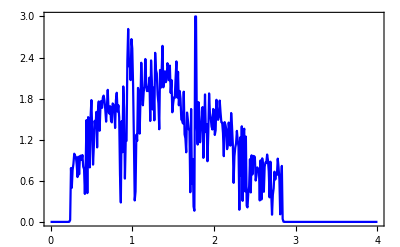

```mathematica
ListLinePlot[Table[{ω,deltae[ω,0.3,0,0]},{ω,Range[0,4,0.01]}],PlotStyle->Blue,Frame->True]
```

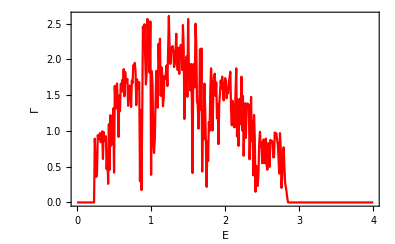

```mathematica
Show[%646,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
{{0.3,3,-4.979435760840324*^7},{0.4,3,-1.8756979415244603*^8},{0.5,3,-1.0144892286546566*^9},{0.6,3,-2.0718974715861052*^8},{0.7,3,-1.5452088156674528*^8},{0.8,3,-1.2754301599058773*^8},{0.9,3,-1.0643049415690829*^8}}
```

{{0.3,3,-4.97944×10^7},{0.4,3,-1.8757×10^8},{0.5,3,-1.01449×10^9},{0.6,3,-2.0719×10^8},{0.7,3,-1.54521×10^8},{0.8,3,-1.27543×10^8},{0.9,3,-1.0643×10^8}}

```mathematica
Transpose[Join[{Transpose[%76][[1]]},{-Transpose[%76][[3]]}]]
```

{{0.3,4.97944×10^7},{0.4,1.8757×10^8},{0.5,1.01449×10^9},{0.6,2.0719×10^8},{0.7,1.54521×10^8},{0.8,1.27543×10^8},{0.9,1.0643×10^8}}

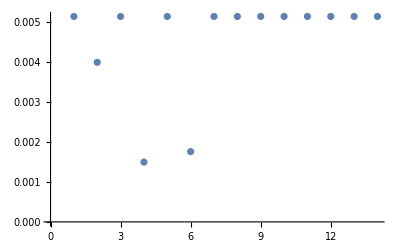

```mathematica
ListPlot[{0.005135517299263662,0.0039891095347190765,0.005135517299263662,0.001494698528317434,0.005135517299263662,0.0017563820501665644,0.005135517299263662,0.005135517299263662,0.005135517299263662,0.005135517299263662,0.005135517299263662,0.005135517299263662,0.005135517299263662,0.005135517299263662}]
```

```mathematica
level=-1.2 10^7
ab=misfita[0.5,2,0.0]
xy=Interpolation[Join[ab[[1]],ab[[2]],ab[[3]],ab[[4]],ab[[5]],ab[[6]],ab[[7]]]]
GraphicsRow[{Plot3D[xy[x,y],{x,0.3,0.9},{y,1,7},(*ContourShading->*)(*PlotLegends->Automatic,*)ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],Axes->{True, True, False}],
ContourPlot[xy[x,y],{x,0.3,0.9},{y,1,7},(*ContourShading->*)ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]}]
Show[Plot3D[xy[x,y],{x,0.3,0.9},{y,1,7},(*ContourShading->*)(*PlotLegends->Automatic,*)ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],Axes->{True, True, False}],Graphics3D[{Texture[ContourPlot[xy[x,y],{x,0.3,0.9},{y,1,7},(*ContourShading->*)ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]],EdgeForm[],Polygon[{{0.3,0.7,level},{0.3,0.7,level},{01,7,level},{1,7,level}},VertexTextureCoordinates->Automatic],Lighting->"Neutral"}],PlotRange->All,BoxRatios->{1,1,.6},FaceGrids->{Back,Left}]
```

-1.2×10^7

{{{0.3,1,-1.14824×10^7},{0.4,1,-3.51477×10^7},{0.5,1,-1.0608×10^8},{0.6,1,-2.75984×10^8},{0.7,1,-5.89173×10^8},{0.8,1,-7.74504×10^8},{0.9,1,-6.83736×10^8}},{{0.3,2,-3.30953×10^7},{0.4,2,-1.74915×10^8},{0.5,2,-7.74654×10^8},{0.6,2,-5.82622×10^8},{0.7,2,-4.18051×10^8},{0.8,2,-2.5825×10^8},{0.9,2,-1.81381×10^8}},{{0.3,3,-7.77941×10^7},{0.4,3,-3.79463×10^8},{0.5,3,-1.1079×10^9},{0.6,3,-2.37451×10^8},{0.7,3,-1.40455×10^8},{0.8,3,-1.06694×10^8},{0.9,3,-8.67444×10^7}},{{0.3,4,-1.3355×10^8},{0.4,4,-3.73231×10^8},{0.5,4,-6.47463×10^8},{0.6,4,-1.22781×10^8},{0.7,4,-7.44079×10^7},{0.8,4,-6.00496×10^7},{0.9,4,-5.89547×10^7}},{{0.3,5,-2.08043×10^8},{0.4,5,-3.15392×10^8},{0.5,5,-3.62849×10^8},{0.6,5,-7.30154×10^7},{0.7,5,-4.90227×10^7},{0.8,5,-4.38412×10^7},{0.9,5,-4.29521×10^7}},{{0.3,6,-2.64359×10^8},{0.4,6,-2.29677×10^8},{0.5,6,-2.31184×10^8},{0.6,6,-5.39457×10^7},{0.7,6,-3.63618×10^7},{0.8,6,-3.36129×10^7},{0.9,6,-3.72657×10^7}},{{0.3,7,-2.30955×10^8},{0.4,7,-2.41966×10^8},{0.5,7,-1.94522×10^8},{0.6,7,-5.6704×10^7},{0.7,7,-4.38016×10^7},{0.8,7,-4.07909×10^7},{0.9,7,-3.94824×10^7}}}

InterpolatingFunction[…]